# ICS Interaction Optimisation + Tuning Curves (Including Hourglass Effect)

Round beam optimisation code (ϵ_x = ϵ_y = ϵ, β_x= β_y=β) for narrow bandwidth flux maximisation. The collimated flux method used in the calculation is my derived collimated flux detailed in my thesis. This code can use RMS or FWHM bandwidth for optimisations and can also do single point (i.e a single bandwidth value) or tuning curve (range of bandwidth) optimisations. The method is completely self derived using the Ranjan bandwidth: N. Ranjan, Simulation of inverse Compton scattering and its implications on the scattered linewidth, PRAB 21, 030701 (2018).

## Setup + Base Equations

## Units, Constants, Cases + Optimisation Parameters

```mathematica
(*Units*)
```

```mathematica
MeV=10^6;
nm=10^-9;
mm=10^-3;
mrad=10^-3;
μrad=10^-6;
nrad=10^-9;
μm=10^-6;
pC=10^-12;
nC=10^-9;
μJ=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
```

```mathematica
me=0.51099895MeV;
h=4.135667696*10^-15; (*in eV*)
clight=299792458;
echarge=1.60217662*10^-19;
σT=6.6524587158*10^-29;
re=2.8179403262*10^-15;
fivedeg=(5*π)/180;
```

```mathematica
(*Cases*)
```

```mathematica
CBETA42 = {Ee->42MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA78 = {Ee->78MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA114= {Ee->114MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA150 = {Ee->150MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
headonCBETA150 = {Ee->150MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->0,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};

DIANA340={Ee->340MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA680={Ee->680MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1020={Ee->1020MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

DIANA347={Ee->347MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->125MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA687={Ee->687MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->125MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1027={Ee->1027MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->125MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

MAXIIIeq={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->1nC,Epulse->120μJ,ϵn->17.5471mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinj={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->1nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinjheadon={Ee->700MeV,λ->1064nm,ϕ->0,Q->1nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};

HighMAXIIIinj={Ee->1520MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};

CLS300NdYAG={Ee->99.71MeV,λ->1064nm,ϕ->0,Q->100pC,Epulse->100μJ,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,ΔEe->8.6*10^-4,Δλ->6.5*10^-4};
CLS300HoYAG={Ee->99.71MeV,λ->2120nm,ϕ->0,Q->100pC,Epulse->100μJ,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,ΔEe->8.6*10^-4,Δλ->6.5*10^-4};
```

```mathematica
(*NEW DIANA*)
DIANA362={Ee->362MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->6.57*10^-4};
DIANA717={Ee->717MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->6.57*10^-4};
DIANA1072={Ee->1072MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->6.57*10^-4};
```

```mathematica
(*Opt + Char Cases*)
CaseA={Ee->1000MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->30μm,tpulse->10ps,σze->1mm,f->100MHz,ΔEe->10^-4,Δλ->4.66*10^-4};
(*Case B is not appropriate for this method*)
CaseC={Ee->25MeV,λ->1064nm,ϕ->fivedeg,Q->10pC,Epulse->100μJ,ϵn->0.1mm mrad,σL->30μm,tpulse->10ps,σze->0.38mm,f->100MHz,ΔEe->3*10^-4,Δλ->4.66*10^-4};
```

```mathematica
trialcase=CBETA42;
```

## Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(h*clight)/λ;
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Scattered Photon Energy

```mathematica
Eγ[Ee_,ϕ_,λ_,θ_]:=(EL[λ]*(1+β[Ee]*Cos[ϕ]))/(1-β[Ee]*Cos[θ]+EL[λ]/Ee*(1+Cos[ϕ+θ]));
```

```mathematica
Eγ[Ee,ϕ,λ,0]/.trialcase
```

32170.4

## Lorentz Invariants (from Mandelstam Variables)

```mathematica
X[Ee_,ϕ_,λ_]:=(2*γ[Ee]*EL[λ]*(1+β[Ee]*Cos[ϕ]))/me;
Y[Ee_,ϕ_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,ϕ,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

```mathematica
X[Ee,ϕ,λ]/.trialcase
```

0.000757362

```mathematica
Y[Ee,ϕ,λ,0]/.trialcase
```

0.000756781

## Cross Section, Luminosity + Collimated Flux

## Cross Section [Berestetskii, σ = f(Y)]

Berestetskii, Pitaevskii and Lifshitz, Quantum Electrodynamics Vol 4 used as reference.

```mathematica
dσdY[Ee_,ϕ_,λ_,θ_]:=(8*π*re^2)/X[Ee,ϕ,λ]^2*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

```mathematica
dσdY[Ee,ϕ,λ,0]/.trialcase
```

1.78252×10^-22

## Lorentz Invariant Y Differential [Me, Y = f(θ)]

```mathematica
dYdθ[Ee_,θ_,ϕ_,λ_]:=(X[Ee,ϕ,λ]*β[Ee]*Sin[θ]*(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)-X[Ee,ϕ,λ]*(1-β[Ee]*Cos[θ])*(β[Ee]*Sin[θ]-EL[λ]/Ee*Sin[ϕ+θ]))/(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)^2;
```

## Cross Section [Me, σ = f(θ)]

```mathematica
dσdθ[Ee_,ϕ_,λ_,θ_]:=dσdY[Ee,ϕ,λ,θ]*dYdθ[Ee,θ,ϕ,λ];
```

```mathematica
Off[NIntegrate::nlim,NIntegrate::inumr];
```

```mathematica
σ[Ee_,ϕ_,λ_,θcol_]:=NIntegrate[dσdθ[Ee,ϕ,λ,θ],{θ,0,θcol},Method->"Trapezoidal"];
```

```mathematica
σ[Ee,ϕ,λ,0.5mrad]/.trialcase//AbsoluteTiming
```

{0.0961313,1.80395×10^-31}

## Collimated Flux Intermediaries

```mathematica
(*Luminosity equations*)
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
zr[σL_,λ_]:=(4*π*σL^2)/λ;
```

## Head-on Luminosity

```mathematica
L[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_]:=(Ne[Q]*NL[Epulse,λ])/(2*π*convxy[βIP,ϵn,Ee,σL]^2);
```

```mathematica
L[Ee,λ,Q,Epulse,0.1,ϵn,σL]/.trialcase
```

1.07105×10^31

## Angular Crossing + Hourglass Effect (Miyahara)

Y. Miyahara, Luminosity of angled collision of strongly focused beams with different Gaussian distributions, NIM A 588 (2008). Benchmarked elsewhere + results in thesis.

```mathematica
H[ϕ_,βIP_,Ee_,ϵn_,σL_,σze_,tpulse_]:=Cos[ϕ/2]*Sqrt[(convxy[βIP,ϵn,Ee,σL]^2*convxy[βIP,ϵn,Ee,σL]^2)/(π*convz[σze,tpulse]^2)];
Ux[βIP_,Ee_,ϵn_,σL_,λ_]:=Sqrt[1/2*(σe[βIP,ϵn,Ee]^2/βIP^2+σL^2/zr[σL,λ]^2)];
Uy[βIP_,Ee_,ϵn_,σL_,λ_]:=Sqrt[1/2*(σe[βIP,ϵn,Ee]^2/βIP^2+σL^2/zr[σL,λ]^2)];
hmiy[ϕ_,βIP_,Ee_,ϵn_,σL_,λ_,σze_,tpulse_,Zc_]:=Sin[ϕ]^2/(convxy[βIP,ϵn,Ee,σL]^2+Ux[βIP,Ee,ϵn,σL,λ]^2*Zc^2)+Cos[ϕ]^2/convz[σze,tpulse]^2;
```

```mathematica
RACHG[ϕ_,βIP_,Ee_,ϵn_,σL_,σze_,tpulse_,λ_]:=NIntegrate[(H[ϕ,βIP,Ee,ϵn,σL,σze,tpulse]*Exp[-hmiy[ϕ,βIP,Ee,ϵn,σL,λ,σze,tpulse,Zc]*Zc^2])/(Sqrt[convxy[βIP,ϵn,Ee,σL]^2+Ux[βIP,Ee,ϵn,σL,λ]^2*Zc^2]*Sqrt[convxy[βIP,ϵn,Ee,σL]^2+Uy[βIP,Ee,ϵn,σL,λ]^2*Zc^2]),{Zc,-0.1,0.1},Method->"Trapezoidal"];
```

```mathematica
RACHG[ϕ,0.1,Ee,ϵn,σL,σze,tpulse,λ]/.trialcase//AbsoluteTiming
```

{0.0104858,0.113165}

## Crab Crossing (Miyahara)

```mathematica
tx[βIP_,ϵn_,Ee_,σL_,λ_,σze_,tpulse_]:=Sqrt[convxy[βIP,ϵn,Ee,σL]^2/(Ux[βIP,Ee,ϵn,σL,λ]^2*convz[σze,tpulse]^2)];
ty[βIP_,ϵn_,Ee_,σL_,λ_,σze_,tpulse_]:=Sqrt[convxy[βIP,ϵn,Ee,σL]^2/(Uy[βIP,Ee,ϵn,σL,λ]^2*convz[σze,tpulse]^2)];
```

```mathematica
RHG[βIP_,ϵn_,Ee_,σL_,λ_,σze_,tpulse_]:=1/Sqrt[π]*NIntegrate[Exp[-t^2]/(Sqrt[1+t^2/tx[βIP,ϵn,Ee,σL,λ,σze,tpulse]^2]*Sqrt[1+t^2/ty[βIP,ϵn,Ee,σL,λ,σze,tpulse]^2]),{t,-5,5},Method->"Trapezoidal"];
```

```mathematica
RCCHG[βIP_,ϵn_,Ee_,σL_,λ_,σze_,tpulse_,ϕ_]:=RHG[βIP,ϵn,Ee,σL,λ,σze,tpulse]*Cos[ϕ];
```

```mathematica
RCCHG[0.1,ϵn,Ee,σL,λ,σze,tpulse,ϕ]/.trialcase//AbsoluteTiming
```

{0.0059368,0.969385}

## Collimated Flux

My collimated flux derivation.

```mathematica
Fcol[Ee_,ϕ_,λ_,θcol_,βIP_,ϵn_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RACHG[ϕ,βIP,Ee,ϵn,σL,σze,tpulse,λ]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

```mathematica
Fcol[Ee,ϕ,λ,0.5mrad,0.1,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase//AbsoluteTiming
```

{0.0187856,3.55303×10^7}

```mathematica
CCFcol[Ee_,ϕ_,λ_,θcol_,βIP_,ϵn_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RCCHG[βIP,ϵn,Ee,σL,λ,σze,tpulse,ϕ]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

```mathematica
CCFcol[Ee,ϕ,λ,0.5mrad,0.1,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase//AbsoluteTiming
```

{0.0241483,3.04358×10^8}

## Flux in a 0.1% BW (FWHM)

```mathematica
σc[Ee_,ϕ_,λ_]:=σT*(1-X[Ee,ϕ,λ]);
```

```mathematica
F01[Ee_,ϕ_,λ_,βIP_,ϵn_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=3/2*10^-3*σc[Ee,ϕ,λ]*RACHG[ϕ,βIP,Ee,ϵn,σL,σze,tpulse,λ]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

## Source Size

```mathematica
σγ[βIP_,ϵn_,Ee_,σL_]:=(σe[βIP,ϵn,Ee]*σL)/Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
```

## Bandwidth

Ranjan et al bandwidth: Ranjan et al, Simulation of inverse Compton scattering and its implications on the scattered linewidth, 21, 030701 (2018).

## Bandwidth Terms

```mathematica
collterm[Ee_,λ_,θ_,ϕ_]:=1/Sqrt[12]*ψ[Ee,θ]^2/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θ_,ϕ_]:=(2+X[Ee,ϕ,λ])/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θ_,ϕ_]:=(1+ψ[Ee,θ]^2)/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2)*Δλ;
emittanceterm[Ee_,ϵn_,ϕ_,λ_,βIP_]:=(2*γ[Ee]*ϵn)/((1+X[Ee,ϕ,λ])*βIP);
```

## Bandwidth

```mathematica
RMSbandwidth[Ee_,λ_,θ_,ϕ_,ΔEe_,Δλ_,ϵn_,βIP_]:=Sqrt[collterm[Ee,λ,θ,ϕ]^2+beamspreadterm[Ee,λ,ΔEe,θ,ϕ]^2+laserspreadterm[Ee,λ,Δλ,θ,ϕ]^2+emittanceterm[Ee,ϵn,ϕ,λ,βIP]^2];
```

```mathematica
FWHMbandwidth[Ee_,λ_,θ_,ϕ_,ΔEe_,Δλ_,ϵn_,βIP_]:=2*Sqrt[2*Log[2]]*RMSbandwidth[Ee,λ,θ,ϕ,ΔEe,Δλ,ϵn,βIP];
```

## β^* Calculation

```mathematica
RMSβstar[Ee_,ϵn_,RMSBW_,λ_,ΔEe_,Δλ_,θ_,ϕ_]:=(2*γ[Ee]*ϵn)/((1+X[Ee,ϕ,λ])*Sqrt[RMSBW^2-(collterm[Ee,λ,θ,ϕ]^2+beamspreadterm[Ee,λ,ΔEe,θ,ϕ]^2+laserspreadterm[Ee,λ,Δλ,θ,ϕ]^2)]);
```

```mathematica
FWHMβstar[Ee_,ϵn_,FWHMBW_,λ_,ΔEe_,Δλ_,θ_,ϕ_]:=(2*γ[Ee]*ϵn)/((1+X[Ee,ϕ,λ])*Sqrt[(FWHMBW/(2*Sqrt[2*Log[2]]))^2-(collterm[Ee,λ,θ,ϕ]^2+beamspreadterm[Ee,λ,ΔEe,θ,ϕ]^2+laserspreadterm[Ee,λ,Δλ,θ,ϕ]^2)]);
```

# RMS Single Fixed Bandwidth Optimisation

```mathematica
(*Optimisation Parameters*)
RMSBW=0.5/100;
θmax=2mrad;
θstep=50nrad;(*100 nrad used for single cases (accurate enough! ~5 min)*)
```

## β^*-θ_col Pairings

```mathematica
RMSβstardat=Table[{θ,Re[RMSβstar[Ee,ϵn,RMSBW,λ,ΔEe,Δλ,θ,ϕ]]/.trialcase},{θ,0,θmax,θstep}]//AbsoluteTiming;
RMSsimtime={RMSβstardat⟦1⟧};
```

```mathematica
RMSimaginarycut=Min[Position[RMSβstardat⟦2⟧⟦All,2⟧,0.]]//AbsoluteTiming;
AppendTo[RMSsimtime,RMSimaginarycut⟦1⟧];
```

```mathematica
RMSβstardat=RMSβstardat⟦2⟧⟦1;;(RMSimaginarycut⟦2⟧-1),All⟧//AbsoluteTiming;
AppendTo[RMSsimtime,RMSβstardat⟦1⟧];
```

β^*is calculated for each step in the range 0 to θmax. The position at which β^* becomes imaginary is found and then the imaginary values are discarded.

## Collimated Flux Maximisation

```mathematica
Off[NIntegrate::izero]
```

```mathematica
RMSFcoldat=Table[{RMSβstardat⟦2⟧⟦i,1⟧,RMSβstardat⟦2⟧⟦i,2⟧,Fcol[Ee,ϕ,λ,RMSβstardat⟦2⟧⟦i,1⟧,RMSβstardat⟦2⟧⟦i,2⟧,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase},{i,1,(RMSimaginarycut⟦2⟧-1),1}]//AbsoluteTiming;
AppendTo[RMSsimtime,RMSFcoldat⟦1⟧];
```

```mathematica
RMSmaxval=Position[RMSFcoldat⟦2⟧⟦All,3⟧,Max[RMSFcoldat⟦2⟧⟦All,3⟧]]⟦1,1⟧;
```

## Results

```mathematica
RMSoptData={RMSBW*100,(100*RMSbandwidth[Ee,λ,RMSFcoldat⟦2⟧⟦RMSmaxval,1⟧,ϕ,ΔEe,Δλ,ϵn,RMSFcoldat⟦2⟧⟦RMSmaxval,2⟧]/.trialcase),(RMSFcoldat⟦2⟧⟦RMSmaxval,1⟧)/mrad//N,RMSFcoldat⟦2⟧⟦RMSmaxval,2⟧,RMSFcoldat⟦2⟧⟦RMSmaxval,3⟧,Total[RMSsimtime]};
```

Data is saved in the same way as shown in the grid for the single case optimisations. {BW_Target, BW_Achieved, θ_col, β^*, F_col,t_sim}

```mathematica
RMSoptGrid=Grid[{{"RMS Optimisation",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"RMS Target Bandwidth","(ΔE_γ/E_γ)_RMS",RMSBW*100,"%"},{"RMS Achieved Bandwidth","(ΔE_γ/E_γ)_RMS",(100*RMSbandwidth[Ee,λ,RMSFcoldat⟦2⟧⟦RMSmaxval,1⟧,ϕ,ΔEe,Δλ,ϵn,RMSFcoldat⟦2⟧⟦RMSmaxval,2⟧]/.trialcase),"%"},{"Collimation Angle","θ_col",(RMSFcoldat⟦2⟧⟦RMSmaxval,1⟧)/mrad//N,"mrad"},{"β-function at the IP","β^*",RMSFcoldat⟦2⟧⟦RMSmaxval,2⟧,"m"},{"Collimated Flux","F_col",RMSFcoldat⟦2⟧⟦RMSmaxval,3⟧,"ph/s"},{"Simulation Time","t_sim",Total[RMSsimtime],"s"}},Dividers->{{True,True,True,True,True},{True,True,True,False,True,False,False,True,True}}]
```

RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
Collimation Angle | θ_col | 0.4335 | mrad
β-function at the IP | β^* | 0.126953 | m
Collimated Flux | F_col | 3.57332×10^8 | ph/s
Simulation Time | t_sim | 131.676 | s

```mathematica
(σe[RMSFcoldat⟦2⟧⟦RMSmaxval,2⟧,ϵn,Ee]/.CBETA150)/μm
```

11.3713

```mathematica
(σγ[RMSFcoldat⟦2⟧⟦RMSmaxval,2⟧,ϵn,Ee,σL]/.CBETA150)/μm
```

10.3508

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Single_Point/1D_RB"];
RMSoptGrid>>"RMSCASEC-0.5BW-Grid.txt";
RMSoptData>>"RMSCASEC-0.5BW-Data.txt";
```

Data saved in particular accelerator’s folder. Naming Convention: <RMS | FWHM><Beam KE>-<BW as %>BW-<Grid | Data>.txt

# FWHM Single Fixed Bandwidth Optimisation

```mathematica
(*Optimisation Parameters*)
FWHMBW=1/100;
θmax=5mrad;
θstep=100nrad;(*100 nrad used for single cases (accurate enough! ~5 min)*)
```

## β^*-θ_col Pairings

```mathematica
FWHMβstardat=Table[{θ,Re[FWHMβstar[Ee,ϵn,FWHMBW,λ,ΔEe,Δλ,θ,ϕ]]/.trialcase},{θ,0,θmax,θstep}]//AbsoluteTiming;
FWHMsimtime={FWHMβstardat⟦1⟧};
```

```mathematica
FWHMimaginarycut=Min[Position[FWHMβstardat⟦2⟧⟦All,2⟧,0.]]//AbsoluteTiming;
AppendTo[FWHMsimtime,FWHMimaginarycut⟦1⟧];
```

```mathematica
FWHMβstardat=FWHMβstardat⟦2⟧⟦1;;(FWHMimaginarycut⟦2⟧-1),All⟧//AbsoluteTiming;
AppendTo[FWHMsimtime,FWHMβstardat⟦1⟧];
```

β^*is calculated for each step in the range 0 to θmax. The position at which β^* becomes imaginary is found and then the imaginary values are discarded.

## Collimated Flux Maximisation

```mathematica
Off[NIntegrate::izero]
```

```mathematica
FWHMFcoldat=Table[{FWHMβstardat⟦2⟧⟦i,1⟧,FWHMβstardat⟦2⟧⟦i,2⟧,Fcol[Ee,ϕ,λ,FWHMβstardat⟦2⟧⟦i,1⟧,FWHMβstardat⟦2⟧⟦i,2⟧,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase},{i,1,(FWHMimaginarycut⟦2⟧-1),1}]//AbsoluteTiming;
AppendTo[FWHMsimtime,FWHMFcoldat⟦1⟧];
```

```mathematica
FWHMmaxval=Position[FWHMFcoldat⟦2⟧⟦All,3⟧,Max[FWHMFcoldat⟦2⟧⟦All,3⟧]]⟦1,1⟧;
```

## Results

```mathematica
FWHMoptData={FWHMBW*100,(100*FWHMbandwidth[Ee,λ,FWHMFcoldat⟦2⟧⟦FWHMmaxval,1⟧,ϕ,ΔEe,Δλ,ϵn,FWHMFcoldat⟦2⟧⟦FWHMmaxval,2⟧]/.trialcase),(FWHMFcoldat⟦2⟧⟦FWHMmaxval,1⟧)/mrad//N,FWHMFcoldat⟦2⟧⟦FWHMmaxval,2⟧,FWHMFcoldat⟦2⟧⟦FWHMmaxval,3⟧,Total[FWHMsimtime]};
```

Data is saved in the same way as shown in the grid for the single case optimisations. {BW_Target, BW_Achieved, θ_col, β^*, F_col,t_sim}

```mathematica
FWHMoptGrid=Grid[{{"FWHM Optimisation",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"FWHM Target Bandwidth","(ΔE_γ/E_γ)_FWHM",FWHMBW*100,"%"},{"FWHM Achieved Bandwidth","(ΔE_γ/E_γ)_FWHM",(100*FWHMbandwidth[Ee,λ,FWHMFcoldat⟦2⟧⟦FWHMmaxval,1⟧,ϕ,ΔEe,Δλ,ϵn,FWHMFcoldat⟦2⟧⟦FWHMmaxval,2⟧]/.trialcase),"%"},{"Collimation Angle","θ_col",(FWHMFcoldat⟦2⟧⟦FWHMmaxval,1⟧)/mrad//N,"mrad"},{"β-function at the IP","β^*",FWHMFcoldat⟦2⟧⟦FWHMmaxval,2⟧,"m"},{"Collimated Flux","F_col",FWHMFcoldat⟦2⟧⟦FWHMmaxval,3⟧,"ph/s"},{"Simulation Time","t_sim",Total[FWHMsimtime],"s"}},Dividers->{{True,True,True,True,True},{True,True,True,False,True,False,False,True,True}}]
```

FWHM Optimisation |  |  | 
Parameter | Symbol | Value | Unit
FWHM Target Bandwidth | (ΔE_γ/E_γ)_FWHM | 1 | %
FWHM Achieved Bandwidth | (ΔE_γ/E_γ)_FWHM | 1. | %
Collimation Angle | θ_col | 0.0574 | mrad
β-function at the IP | β^* | 1.22858 | m
Collimated Flux | F_col | 2.97728×10^9 | ph/s
Simulation Time | t_sim | 34.6594 | s

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/DIANA Optimisations"];
FWHMoptGrid>>"FWHM1027-1BW-Grid.txt";
FWHMoptData>>"FWHM1027-1BW-Data.txt";
```

Data saved in particular accelerator’s folder. Naming Convention: <RMS | FWHM><Beam KE>-<BW as %>BW-<Grid | Data>.txt

# Single FWHM vs RMS Comparison

## Optimised Values Comparison (Round Beams)

```mathematica
Grid[{{RMSopt,FWHMopt}}]
```

RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
Collimation Angle | θ_col | 0.0937 | mrad
β-function at the IP | β^* | 0.721065 | m
Collimated Flux | F_col | 2.92926×10^9 | ph/s
Simulation Time | t_sim | 31.187 | s | FWHM Optimisation |  |  | 
Parameter | Symbol | Value | Unit
FWHM Target Bandwidth | (ΔE_γ/E_γ)_FWHM | 0.5 | %
FWHM Achieved Bandwidth | (ΔE_γ/E_γ)_FWHM | 0.5 | %
Collimation Angle | θ_col | 0.055 | mrad
β-function at the IP | β^* | 1.6067 | m
Collimated Flux | F_col | 8.63719×10^8 | ph/s
Simulation Time | t_sim | 29.528 | s

# RMS Tuning Curve Optimisation

Typically use ~2000 points in the optimisation, which takes ~2 hours.

```mathematica
(*Optimisation Parameters*)
rmsBWmin=Sqrt[(2*ΔEe/.trialcase)^2+(Δλ/.trialcase)^2]; 
rmsBWmax=1/100;
rmsBWstep=10^-3/100;
rmsθmax=5.0mrad;
rmsθstep=0.5μrad;
```

## β^*-θ_col Pairings

Nested computations like nested tables can’t both be parallelized. Therefore, only the inner table (the more computationally intensive) is parallelized.

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[RMSβstar,rmsBWmin,rmsBWmax,rmsBWstep,rmsθmax,rmsθstep];
```

```mathematica
RMSβstardatcurve=Table[{BW,ParallelTable[{θ,Re[RMSβstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ,ϕ]]/.trialcase},{θ,0,rmsθmax,rmsθstep}]},{BW,rmsBWmin,rmsBWmax,rmsBWstep}]//AbsoluteTiming;
```

```mathematica
RMSsimtime={RMSβstardatcurve⟦1⟧};
```

```mathematica
CloseKernels[];
```

```mathematica
RMSimaginarycuts=Table[Min[Position[RMSβstardatcurve⟦2⟧⟦i,2⟧⟦All,2⟧,0.]],{i,1,((rmsBWmax-rmsBWmin)/rmsBWstep)}]//AbsoluteTiming;
AppendTo[RMSsimtime,RMSimaginarycuts⟦1⟧];
```

```mathematica
RMSβstardatcurve=Table[{RMSβstardatcurve⟦2⟧⟦i,1⟧,RMSβstardatcurve⟦2⟧⟦i,2⟧⟦1;;(RMSimaginarycuts⟦2⟧⟦i⟧-1),All⟧},{i,1,((rmsBWmax-rmsBWmin)/rmsBWstep)}]//AbsoluteTiming;
AppendTo[RMSsimtime,RMSβstardatcurve⟦1⟧];
```

## Collimated Flux Maximisation

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[Fcol,RMSFcoldatcurve,RMSβstardatcurve,RMSimaginarycuts,rmsBWmax,rmsBWmin,rmsBWstep];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::izero,NIntegrate::nlim,NIntegrate::inumr]];
```

```mathematica
RMSFcoldatcurve=Table[{RMSβstardatcurve⟦2⟧⟦i,1⟧,ParallelTable[{RMSβstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,RMSβstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,Fcol[Ee,ϕ,λ,RMSβstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,RMSβstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase},{j,1,(RMSimaginarycuts⟦2⟧⟦i⟧-1)}]},{i,1,((rmsBWmax-rmsBWmin)/rmsBWstep)}]//AbsoluteTiming;
```

```mathematica
AppendTo[RMSsimtime,RMSFcoldatcurve⟦1⟧];
```

```mathematica
CloseKernels[];
```

```mathematica
RMSmaxvals=Table[Position[RMSFcoldatcurve⟦2⟧⟦i,2⟧⟦All,3⟧,Max[RMSFcoldatcurve⟦2⟧⟦i,2⟧⟦All,3⟧]]⟦1,1⟧,{i,1,((rmsBWmax-rmsBWmin)/rmsBWstep)}]//AbsoluteTiming;
AppendTo[RMSsimtime,RMSmaxvals⟦1⟧];
```

```mathematica
RMSmaxdata=Table[{RMSFcoldatcurve⟦2⟧⟦i,1⟧*100,(RMSFcoldatcurve⟦2⟧⟦All,2⟧⟦i,RMSmaxvals⟦2⟧⟦i⟧,1⟧)/mrad,RMSFcoldatcurve⟦2⟧⟦All,2⟧⟦i,RMSmaxvals⟦2⟧⟦i⟧,2⟧,RMSFcoldatcurve⟦2⟧⟦All,2⟧⟦i,RMSmaxvals⟦2⟧⟦i⟧,3⟧},{i,1,((rmsBWmax-rmsBWmin)/rmsBWstep)}]//AbsoluteTiming;
AppendTo[RMSsimtime,RMSmaxdata⟦1⟧];
```

The maxdata array is of the form BW, θcol, β^*, F_ψ . All of the necessary data is available in this singular array.

## Saving Data

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/Thesis"];
RMSmaxdata⟦2⟧>>"CBETA42optRMS.txt";
```

## Timing Data

```mathematica
Total[RMSsimtime]/60
```

279.786

```mathematica
RMSsimtime
```

{1077.31,7.2771,4.3916,15692.,4.12712,2.0119}

## Tuning Curve Plots

```mathematica
RMSFcolBWplot=ListLinePlot[Partition[Riffle[RMSmaxdata⟦2⟧⟦All,1⟧,RMSmaxdata⟦2⟧⟦All,4⟧],2],Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium];
```

```mathematica
RMSβθplot=ListLinePlot[Partition[Riffle[RMSmaxdata⟦2⟧⟦All,2⟧,RMSmaxdata⟦2⟧⟦All,3⟧],2],Frame->True,FrameLabel->{"Collimation Angle [mrad]","β^*-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->All,ImageSize->Medium];
```

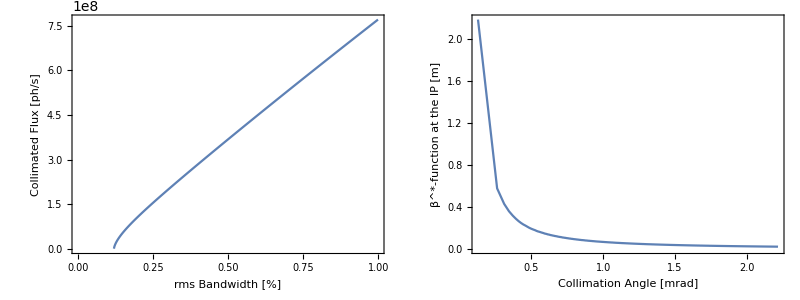

```mathematica
RMSplots=Grid[{{RMSFcolBWplot,RMSβθplot}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/Thesis/Thesis_Plots"];
Export["CBETA42_RB_Fcol_BW.pdf",RMSFcolBWplot];
Export["CBETA42_RB_Beta_Theta.pdf",RMSβθplot];
Export["CBETA42_RB_Tuning_Curves.pdf",RMSplots];
```

# Crab Crossing RMS Tuning Curve Optimisation

```mathematica
(*Optimisation Parameters*)
CCrmsBWmin=Sqrt[(2*ΔEe/.trialcase)^2+(Δλ/.trialcase)^2]; 
CCrmsBWmax=1/100;
CCrmsBWstep=10^-3/100;
CCrmsθmax=0.1mrad;
CCrmsθstep=0.05μrad;(*0.1μrad typically used for tuning curves, 0.32μrad takes 2hrs*)
```

## β^*-θ_col Pairings

Nested computations like nested tables can’t both be parallelized. Therefore, only the inner table (the more computationally intensive) is parallelized.

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[RMSβstar,CCrmsBWmin,CCrmsBWmax,CCrmsBWstep,CCrmsθmax,CCrmsθstep];
```

```mathematica
CCRMSβstardatcurve=Table[{BW,ParallelTable[{θ,Re[RMSβstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ,ϕ]]/.trialcase},{θ,0,CCrmsθmax,CCrmsθstep}]},{BW,CCrmsBWmin,CCrmsBWmax,CCrmsBWstep}]//AbsoluteTiming;
```

```mathematica
CCRMSsimtime={CCRMSβstardatcurve⟦1⟧};
```

```mathematica
CloseKernels[];
```

```mathematica
CCRMSimaginarycuts=Table[Min[Position[CCRMSβstardatcurve⟦2⟧⟦i,2⟧⟦All,2⟧,0.]],{i,1,((CCrmsBWmax-CCrmsBWmin)/CCrmsBWstep)}]//AbsoluteTiming;
AppendTo[CCRMSsimtime,CCRMSimaginarycuts⟦1⟧];
```

```mathematica
CCRMSβstardatcurve=Table[{CCRMSβstardatcurve⟦2⟧⟦i,1⟧,CCRMSβstardatcurve⟦2⟧⟦i,2⟧⟦1;;(CCRMSimaginarycuts⟦2⟧⟦i⟧-1),All⟧},{i,1,((CCrmsBWmax-CCrmsBWmin)/CCrmsBWstep)}]//AbsoluteTiming;
AppendTo[CCRMSsimtime,CCRMSβstardatcurve⟦1⟧];
```

## Collimated Flux Maximisation

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[CCFcol,CCRMSFcoldatcurve,CCRMSβstardatcurve,CCRMSimaginarycuts,CCrmsBWmax,CCrmsBWmin,CCrmsBWstep];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::izero,NIntegrate::nlim,NIntegrate::inumr]];
```

```mathematica
CCRMSFcoldatcurve=Table[{CCRMSβstardatcurve⟦2⟧⟦i,1⟧,ParallelTable[{CCRMSβstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,CCRMSβstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,CCFcol[Ee,ϕ,λ,CCRMSβstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,CCRMSβstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase},{j,1,(CCRMSimaginarycuts⟦2⟧⟦i⟧-1)}]},{i,1,((CCrmsBWmax-CCrmsBWmin)/CCrmsBWstep)}]//AbsoluteTiming;
```

```mathematica
AppendTo[CCRMSsimtime,CCRMSFcoldatcurve⟦1⟧];
```

```mathematica
CloseKernels[];
```

```mathematica
CCRMSmaxvals=Table[Position[CCRMSFcoldatcurve⟦2⟧⟦i,2⟧⟦All,3⟧,Max[CCRMSFcoldatcurve⟦2⟧⟦i,2⟧⟦All,3⟧]]⟦1,1⟧,{i,1,((CCrmsBWmax-CCrmsBWmin)/CCrmsBWstep)}]//AbsoluteTiming;
AppendTo[CCRMSsimtime,CCRMSmaxvals⟦1⟧];
```

```mathematica
CCRMSmaxdata=Table[{CCRMSFcoldatcurve⟦2⟧⟦i,1⟧*100,(CCRMSFcoldatcurve⟦2⟧⟦All,2⟧⟦i,CCRMSmaxvals⟦2⟧⟦i⟧,1⟧)/mrad,CCRMSFcoldatcurve⟦2⟧⟦All,2⟧⟦i,CCRMSmaxvals⟦2⟧⟦i⟧,2⟧,CCRMSFcoldatcurve⟦2⟧⟦All,2⟧⟦i,CCRMSmaxvals⟦2⟧⟦i⟧,3⟧},{i,1,((CCrmsBWmax-CCrmsBWmin)/CCrmsBWstep)}]//AbsoluteTiming;
AppendTo[CCRMSsimtime,CCRMSmaxdata⟦1⟧];
```

The maxdata array is of the form BW, θcol, β^*, F_ψ . All of the necessary data is available in this singular array.

## Saving Data

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA"];
CCRMSmaxdata⟦2⟧>>"DIANA1072optRMSCC.txt";
```

## Timing Data

```mathematica
Total[CCRMSsimtime]/60
```

142.03

```mathematica
CCRMSsimtime
```

{260.235,1.24998,0.787866,8256.93,1.60221,0.966064}

## Tuning Curve Plots

```mathematica
CCRMSFcolBWplot=ListLinePlot[Partition[Riffle[CCRMSmaxdata⟦2⟧⟦All,1⟧,CCRMSmaxdata⟦2⟧⟦All,4⟧],2],Frame->True,FrameLabel->{"rms Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
```

```mathematica
CCRMSβθplot=ListLinePlot[Partition[Riffle[CCRMSmaxdata⟦2⟧⟦All,2⟧,CCRMSmaxdata⟦2⟧⟦All,3⟧],2],Frame->True,FrameLabel->{"Collimation Angle (mrad))","β function at the IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->All,ImageSize->Medium];
```

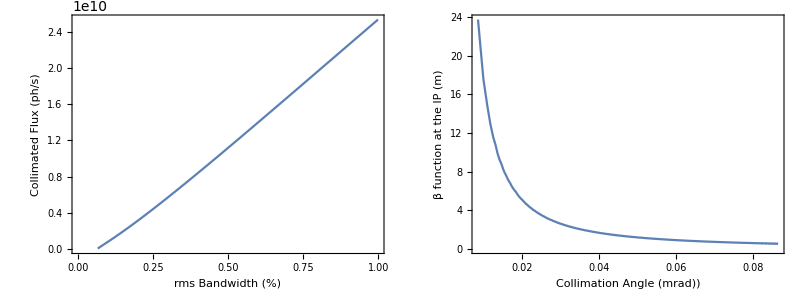

```mathematica
Grid[{{CCRMSFcolBWplot,CCRMSβθplot}}]
```

# FWHM Tuning Curve Optimisation

```mathematica
(*Optimisation Parameters*)
fwhmBWmin=2*Sqrt[2*Log[2]]*Sqrt[(2*ΔEe/.trialcase)^2+(Δλ/.trialcase)^2]; 
fwhmBWmax=1/100;
fwhmBWstep=10^-3/100;
fwhmθmax=2mrad;
fwhmθstep=0.32μrad;(*0.1μrad typically used for tuning curves, 0.32μrad takes 2hrs*)
```

## β^*-θ_col Pairings

Nested computations like nested tables can’t both be parallelized. Therefore, only the inner table (the more computationally intensive) is parallelized.

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[FWHMβstar,fwhmBWmin,fwhmBWmax,fwhmBWstep,fwhmθmax,fwhmθstep];
```

```mathematica
FWHMβstardatcurve=Table[{BW,ParallelTable[{θ,Re[FWHMβstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ,ϕ]]/.trialcase},{θ,0,fwhmθmax,fwhmθstep}]},{BW,fwhmBWmin,fwhmBWmax,fwhmBWstep}]//AbsoluteTiming;
```

```mathematica
FWHMsimtime={FWHMβstardatcurve⟦1⟧};
```

```mathematica
CloseKernels[];
```

```mathematica
FWHMimaginarycuts=Table[Min[Position[FWHMβstardatcurve⟦2⟧⟦i,2⟧⟦All,2⟧,0.]],{i,1,((fwhmBWmax-fwhmBWmin)/fwhmBWstep)}]//AbsoluteTiming;
AppendTo[FWHMsimtime,FWHMimaginarycuts⟦1⟧];
```

```mathematica
FWHMβstardatcurve=Table[{FWHMβstardatcurve⟦2⟧⟦i,1⟧,FWHMβstardatcurve⟦2⟧⟦i,2⟧⟦1;;(FWHMimaginarycuts⟦2⟧⟦i⟧-1),All⟧},{i,1,((fwhmBWmax-fwhmBWmin)/fwhmBWstep)}]//AbsoluteTiming;
AppendTo[FWHMsimtime,FWHMβstardatcurve⟦1⟧];
```

## Collimated Flux Maximisation

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[Fcol,FWHMFcoldatcurve,FWHMβstardatcurve,FWHMimaginarycuts,fwhmBWmax,fwhmBWmin,fwhmBWstep];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::izero,NIntegrate::nlim,NIntegrate::inumr]];
```

```mathematica
FWHMFcoldatcurve=Table[{FWHMβstardatcurve⟦2⟧⟦i,1⟧,ParallelTable[{FWHMβstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,FWHMβstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,Fcol[Ee,ϕ,λ,FWHMβstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,FWHMβstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase},{j,1,(FWHMimaginarycuts⟦2⟧⟦i⟧-1)}]},{i,1,((fwhmBWmax-fwhmBWmin)/fwhmBWstep)}]//AbsoluteTiming;
```

```mathematica
AppendTo[FWHMsimtime,FWHMFcoldatcurve⟦1⟧];
```

```mathematica
CloseKernels[];
```

```mathematica
FWHMmaxvals=Table[Position[FWHMFcoldatcurve⟦2⟧⟦i,2⟧⟦All,3⟧,Max[FWHMFcoldatcurve⟦2⟧⟦i,2⟧⟦All,3⟧]]⟦1,1⟧,{i,1,((fwhmBWmax-fwhmBWmin)/fwhmBWstep)}]//AbsoluteTiming;
AppendTo[FWHMsimtime,FWHMmaxvals⟦1⟧];
```

```mathematica
FWHMmaxdata=Table[{FWHMFcoldatcurve⟦2⟧⟦i,1⟧*100,(FWHMFcoldatcurve⟦2⟧⟦All,2⟧⟦i,FWHMmaxvals⟦2⟧⟦i⟧,1⟧)/mrad,FWHMFcoldatcurve⟦2⟧⟦All,2⟧⟦i,FWHMmaxvals⟦2⟧⟦i⟧,2⟧,FWHMFcoldatcurve⟦2⟧⟦All,2⟧⟦i,FWHMmaxvals⟦2⟧⟦i⟧,3⟧},{i,1,((fwhmBWmax-fwhmBWmin)/fwhmBWstep)}]//AbsoluteTiming;
AppendTo[FWHMsimtime,FWHMmaxdata⟦1⟧];
```

The maxdata array is of the form BW, θcol, β^*, F_ψ . All of the necessary data is available in this singular array.

## Saving Data

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/CBETA"];
FWHMmaxdata⟦2⟧>>"CBETA150optFWHM.txt";
```

## Timing Data

```mathematica
Total[FWHMsimtime]/60
```

70.8737

```mathematica
FWHMsimtime
```

{714.365,3.43043,1.8903,3531.19,0.987248,0.558721}

## Tuning Curve Plots

```mathematica
FWHMFcolBWplot=ListLinePlot[Partition[Riffle[FWHMmaxdata⟦2⟧⟦All,1⟧,FWHMmaxdata⟦2⟧⟦All,4⟧],2],Frame->True,FrameLabel->{"FWHM Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
```

```mathematica
FWHMβθplot=ListLinePlot[Partition[Riffle[FWHMmaxdata⟦2⟧⟦All,2⟧,FWHMmaxdata⟦2⟧⟦All,3⟧],2],Frame->True,FrameLabel->{"Collimation Angle (mrad))","β function at the IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->All,ImageSize->Medium];
```

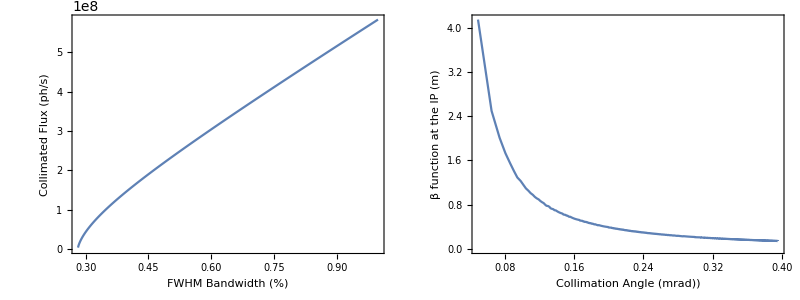

```mathematica
Grid[{{FWHMFcolBWplot,FWHMβθplot}}]
```

# Single Case Tables

## DIANA 0.5% BW Cases

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/DIANA Optimisations"];
DIANA347RMS05=<<"RMS347-0.5BW-Grid.txt";
DIANA347FWHM05=<<"FWHM347-0.5BW-Grid.txt";
DIANA687RMS05=<<"RMS687-0.5BW-Grid.txt";
DIANA687FWHM05=<<"FWHM687-0.5BW-Grid.txt";
DIANA1027RMS05=<<"RMS1027-0.5BW-Grid.txt";
DIANA1027FWHM05=<<"FWHM1027-0.5BW-Grid.txt";
```

```mathematica
Grid[{{DIANA347RMS05,DIANA347FWHM05},{DIANA687RMS05,DIANA687FWHM05},{DIANA1027RMS05,DIANA1027FWHM05}}]
```

RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
Collimation Angle | θ_col | 0.1847 | mrad
β-function at the IP | β^* | 0.364475 | m
Collimated Flux | F_col | 3.68807×10^9 | ph/s
Simulation Time | t_sim | 48.2656 | s | FWHM Optimisation |  |  | 
Parameter | Symbol | Value | Unit
FWHM Target Bandwidth | (ΔE_γ/E_γ)_FWHM | 0.5 | %
FWHM Achieved Bandwidth | (ΔE_γ/E_γ)_FWHM | 0.5 | %
Collimation Angle | θ_col | 0.1084 | mrad
β-function at the IP | β^* | 0.81902 | m
Collimated Flux | F_col | 1.08471×10^9 | ph/s
Simulation Time | t_sim | 42.4332 | s
RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
Collimation Angle | θ_col | 0.0937 | mrad
β-function at the IP | β^* | 0.721065 | m
Collimated Flux | F_col | 3.66158×10^9 | ph/s
Simulation Time | t_sim | 34.3879 | s | FWHM Optimisation |  |  | 
Parameter | Symbol | Value | Unit
FWHM Target Bandwidth | (ΔE_γ/E_γ)_FWHM | 0.5 | %
FWHM Achieved Bandwidth | (ΔE_γ/E_γ)_FWHM | 0.5 | %
Collimation Angle | θ_col | 0.055 | mrad
β-function at the IP | β^* | 1.6067 | m
Collimated Flux | F_col | 1.07965×10^9 | ph/s
Simulation Time | t_sim | 33.2258 | s
RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
Collimation Angle | θ_col | 0.0629 | mrad
β-function at the IP | β^* | 1.07315 | m
Collimated Flux | F_col | 3.64133×10^9 | ph/s
Simulation Time | t_sim | 30.2108 | s | FWHM Optimisation |  |  | 
Parameter | Symbol | Value | Unit
FWHM Target Bandwidth | (ΔE_γ/E_γ)_FWHM | 0.5 | %
FWHM Achieved Bandwidth | (ΔE_γ/E_γ)_FWHM | 0.5 | %
Collimation Angle | θ_col | 0.037 | mrad
β-function at the IP | β^* | 2.40949 | m
Collimated Flux | F_col | 1.07646×10^9 | ph/s
Simulation Time | t_sim | 29.6046 | s

## DIANA 1% BW Cases

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/DIANA Optimisations"];
DIANA347RMS1=<<"RMS347-1BW-Grid.txt";
DIANA347FWHM1=<<"FWHM347-1BW-Grid.txt";
DIANA687RMS1=<<"RMS687-1BW-Grid.txt";
DIANA687FWHM1=<<"FWHM687-1BW-Grid.txt";
DIANA1027RMS1=<<"RMS1027-1BW-Grid.txt";
DIANA1027FWHM1=<<"FWHM1027-1BW-Grid.txt";
```

```mathematica
Grid[{{DIANA347RMS1,DIANA347FWHM1},{DIANA687RMS1,DIANA687FWHM1},{DIANA1027RMS1,DIANA1027FWHM1}}]
```

RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 1 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 1. | %
Collimation Angle | θ_col | 0.2685 | mrad
β-function at the IP | β^* | 0.212681 | m
Collimated Flux | F_col | 8.10935×10^9 | ph/s
Simulation Time | t_sim | 61.8549 | s | FWHM Optimisation |  |  | 
Parameter | Symbol | Value | Unit
FWHM Target Bandwidth | (ΔE_γ/E_γ)_FWHM | 1 | %
FWHM Achieved Bandwidth | (ΔE_γ/E_γ)_FWHM | 1. | %
Collimation Angle | θ_col | 0.1685 | mrad
β-function at the IP | β^* | 0.416763 | m
Collimated Flux | F_col | 3.0142×10^9 | ph/s
Simulation Time | t_sim | 51.8811 | s
RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 1 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 1. | %
Collimation Angle | θ_col | 0.1361 | mrad
β-function at the IP | β^* | 0.416736 | m
Collimated Flux | F_col | 8.04672×10^9 | ph/s
Simulation Time | t_sim | 41.9142 | s | FWHM Optimisation |  |  | 
Parameter | Symbol | Value | Unit
FWHM Target Bandwidth | (ΔE_γ/E_γ)_FWHM | 1 | %
FWHM Achieved Bandwidth | (ΔE_γ/E_γ)_FWHM | 1. | %
Collimation Angle | θ_col | 0.0855 | mrad
β-function at the IP | β^* | 0.82544 | m
Collimated Flux | F_col | 2.99318×10^9 | ph/s
Simulation Time | t_sim | 40.7422 | s
RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 1 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 1. | %
Collimation Angle | θ_col | 0.0914 | mrad
β-function at the IP | β^* | 0.62624 | m
Collimated Flux | F_col | 7.99735×10^9 | ph/s
Simulation Time | t_sim | 34.7376 | s | FWHM Optimisation |  |  | 
Parameter | Symbol | Value | Unit
FWHM Target Bandwidth | (ΔE_γ/E_γ)_FWHM | 1 | %
FWHM Achieved Bandwidth | (ΔE_γ/E_γ)_FWHM | 1. | %
Collimation Angle | θ_col | 0.0574 | mrad
β-function at the IP | β^* | 1.22858 | m
Collimated Flux | F_col | 2.97728×10^9 | ph/s
Simulation Time | t_sim | 34.6594 | s

# Multiple Case Plots

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## CBETA 150 MeV rms

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/CBETA"];
CBETA150rmsDAT=<<"CBETA150optRMS.txt";
CBETA150fwhmDAT=<<"CBETA150optFWHM.txt";
```

```mathematica
CBETA150RMSFBW=ListLinePlot[Partition[Riffle[CBETA150rmsDAT⟦All,1⟧,CBETA150rmsDAT⟦All,4⟧],2],Frame->True,PlotLabel->"0.5% rms BW Optimisation",FrameLabel->{"rms Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
CBETA150RMSβθ=ListLinePlot[Partition[Riffle[CBETA150rmsDAT⟦All,2⟧,CBETA150rmsDAT⟦All,3⟧],2],Frame->True,PlotLabel->"0.5% rms BW Optimisation",FrameLabel->{"Collimation Angle (mrad)","β function at the IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->All,ImageSize->Medium];
```

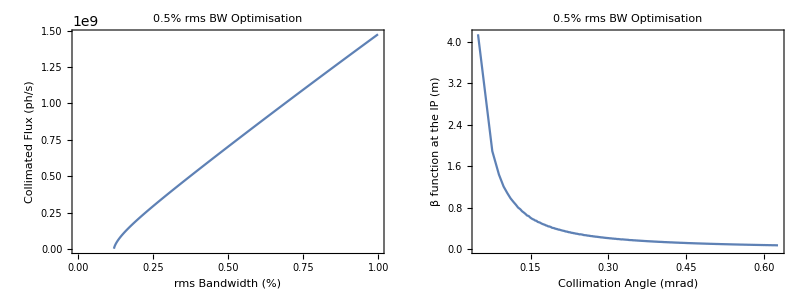

```mathematica
Grid[{{CBETA150RMSFBW,CBETA150RMSβθ}}]
```

## CBETA 150 MeV FWHM

```mathematica
CBETA150FWHMFBW=ListLinePlot[Partition[Riffle[CBETA150fwhmDAT⟦All,1⟧,CBETA150fwhmDAT⟦All,4⟧],2],Frame->True,PlotLabel->"0.5% FWHM BW Optimisation",FrameLabel->{"FWHM Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
CBETA150FWHMβθ=ListLinePlot[Partition[Riffle[CBETA150fwhmDAT⟦All,2⟧,CBETA150fwhmDAT⟦All,3⟧],2],Frame->True,PlotLabel->"0.5% FWHM BW Optimisation",FrameLabel->{"Collimation Angle (mrad)","β function at the IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->All,ImageSize->Medium];
```

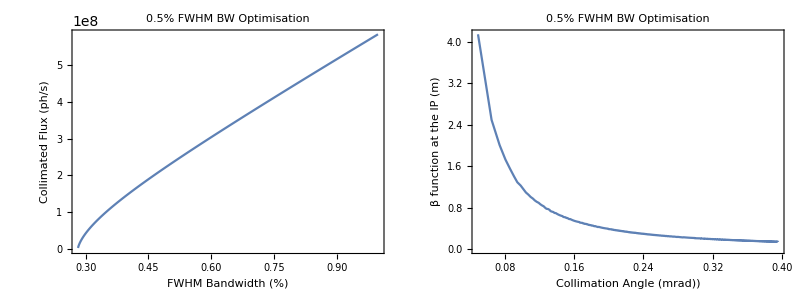

```mathematica
Grid[{{CBETA150FWHMFBW,CBETA150FWHMβθ}}]
```

## CBETA 150 MeV rms vs FWHM

```mathematica
CBETA150RMSFWHMFBW=ListLinePlot[{Partition[Riffle[CBETA150rmsDAT⟦All,1⟧,CBETA150rmsDAT⟦All,4⟧],2],Partition[Riffle[CBETA150fwhmDAT⟦All,1⟧,CBETA150fwhmDAT⟦All,4⟧],2]},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"0.5% BW Optimisations",FrameLabel->{"Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"rms 0.5% BW","FWHM 0.5% BW"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],ImageSize->Medium];
```

```mathematica
CBETA150RMSFWHMβθ=ListLinePlot[{Partition[Riffle[CBETA150rmsDAT⟦All,2⟧,CBETA150rmsDAT⟦All,3⟧],2],Partition[Riffle[CBETA150fwhmDAT⟦All,2⟧,CBETA150fwhmDAT⟦All,3⟧],2]},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"0.5% BW Optimisations",FrameLabel->{"Collimation Angle (mrad)","β function at the IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->{{0.03,0.5},{0,4.3}},PlotLegends->Placed[LineLegend[{"rms 0.5% BW","FWHM 0.5% BW"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.8}],ImageSize->Medium];
```

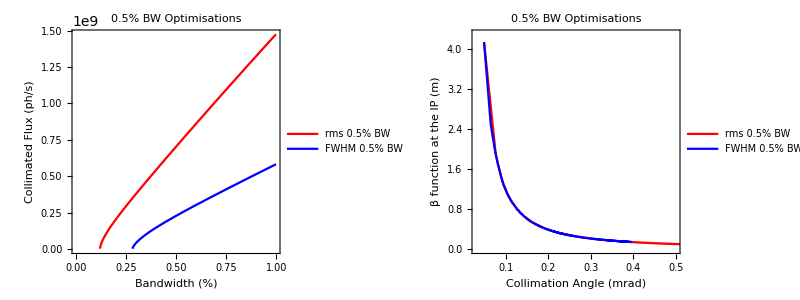

```mathematica
Grid[{{CBETA150RMSFWHMFBW,CBETA150RMSFWHMβθ}}]
```

## CBETA Multiple Energies

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/Thesis"];
CBETA42βθ=<<"CBETA42optRMS.txt";
CBETA78βθ=<<"CBETA78optRMS.txt";
CBETA114βθ=<<"CBETA114optRMS.txt";
CBETA150βθ=<<"CBETA150optRMS.txt";
```

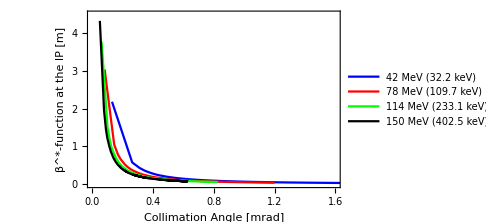

```mathematica
CBETAβθcombined=ListLinePlot[{Partition[Riffle[CBETA42βθ⟦All,2⟧,CBETA42βθ⟦All,3⟧],2],Partition[Riffle[CBETA78βθ⟦All,2⟧,CBETA78βθ⟦All,3⟧],2],Partition[Riffle[CBETA114βθ⟦All,2⟧,CBETA114βθ⟦All,3⟧],2],Partition[Riffle[CBETA150βθ⟦All,2⟧,CBETA150βθ⟦All,3⟧],2]},PlotStyle->{Blue,Red,Green,Black},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β^*-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"42 MeV (32.2 keV)","78 MeV (109.7 keV)","114 MeV (233.1 keV)","150 MeV (402.5 keV)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.7,0.7}],PlotRange->{{0,1.6},{0,4.5}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/Thesis/Thesis_Plots"];
Export["CBETA_COMBINED_beta_theta.pdf",CBETAβθcombined];
```